# Aufgabe H5

## Teilaufgabe (a)

```mathematica
HermiteH[0,x]
```

1

```mathematica
HermiteH[1,x]
```

2 x

```mathematica
HermiteH[2,x]
```

-2+4 x^2

```mathematica
HermiteH[3,x]
```

-12 x+8 x^3

```mathematica
HermiteH[4,x]
```

12-48 x^2+16 x^4

```mathematica
D[HermiteH[n,x],x]
```

2 n HermiteH[-1+n,x]

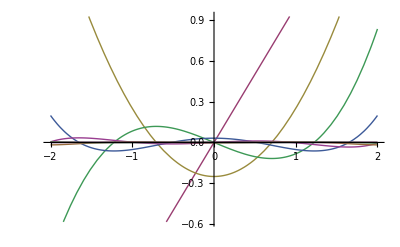

```mathematica
Plot[Evaluate[Table[HermiteH[n,x]/(2^n Factorial[n]),{n,0,10}]],{x,-2,2}]
```